```mathematica
ClearAll["Global`*"];
```

```mathematica
<<QMB`
<<QuantumWalks`
<<QWMisc`
<<Matex`
```

## Funciones

```mathematica
LimitDistribution[TimeStatesList_List,CoinDim_Integer]:=Module[{MeanProbabilities},
MeanProbabilities=Mean[Abs[TimeStatesList]^2];
Total[Partition[MeanProbabilities,CoinDim],{2}]];

Options[DiscreteProbabilityPlot]=Join[Options[ArrayPlot],{"ProbabilityScale"->"Linear"}];
DiscreteProbabilityPlot[GridData_Association,Probabilities_List,Opts:OptionsPattern[]]:=Module[{Coords,MinX,MaxX,MinY,MaxY,NumRows,NumCols,SparseRules,BoundingBoxMatrix,ScaleOption,ProcessedProbabilities},Coords=GridData["Coords"];
ScaleOption=OptionValue["ProbabilityScale"];
(*Transform probabilities based on the selected scale option*)ProcessedProbabilities=Switch[ScaleOption,"Linear",Probabilities,"Squared",Probabilities^2,"Log",Log10[Max[#,10^-12]]&/@Probabilities,_,Probabilities];
{MinX,MaxX}=MinMax[Coords[[All,1]]];
{MinY,MaxY}=MinMax[Coords[[All,2]]];
NumCols=MaxX-MinX+1;
NumRows=MaxY-MinY+1;
(*Map coordinates to matrix indices*)SparseRules=MapThread[{#1[[2]]-MinY+1,#1[[1]]-MinX+1}->#2&,{Coords,ProcessedProbabilities}];
BoundingBoxMatrix=Normal[SparseArray[SparseRules,{NumRows,NumCols},Missing[]]];
ArrayPlot[BoundingBoxMatrix,DataReversed->True,ColorFunction->"SunsetColors",ColorFunctionScaling->True,PlotLegends->Automatic,Frame->True,FrameTicks->Automatic,Mesh->All,MeshStyle->Directive[Opacity[0.15],Gray],Sequence@@FilterRules[{Opts},Options[ArrayPlot]]]];
```

Se estudiaran distintos operadores de moneda aplicadas al shift condicional que contempla condiciones de frontera. 
Las condiciones de frontera se establecen según el tipo de estadio a trabajar.
El 1/8 de Sinai resulta un buen caso para estudiar un caso integrable, R = 0, asi como un caso caótico, R  >> 0

## Grover Coin

## Rectangle

Dimension del operador evolución: 10404

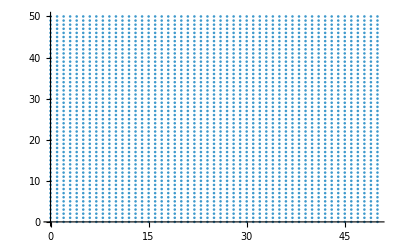

```mathematica
Lx=50;Ly=50;
GrvAngle=Pi/4.;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedGroverCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{RandomInteger[{0,100}],RandomInteger[{0,70}]},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
PhasesWithoutFlatBands=Select[eigenphases,10^-5<Abs[#]<Pi-10^-5&];
FilteredPhases=Pick[PhasesWithoutFlatBands,Prepend[UnitStep[Differences[PhasesWithoutFlatBands]-10^-8],1],1];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

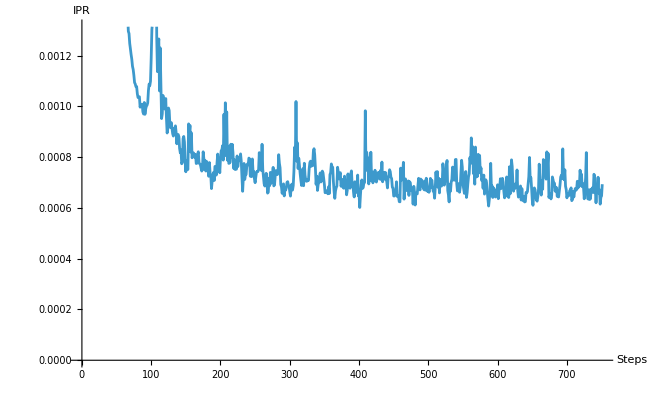

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Sinai

Dimension del operador evolución: 21560

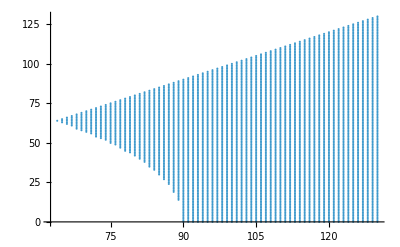

```mathematica
Lx=130;Ly=90;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedGroverCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Sinai.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{40,10},{-1,-1,1,1}//Normalize];
Steps=10;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

Part::partd: Part specification Frames⟦8⟧ is longer than depth of object.

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
PhasesWithoutFlatBands=Select[eigenphases,10^-5<Abs[#]<Pi-10^-5&];
FilteredPhases=Pick[PhasesWithoutFlatBands,Prepend[UnitStep[Differences[PhasesWithoutFlatBands]-10^-8],1],1];
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Triangle_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Sinai_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_Chaos.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{100,40},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

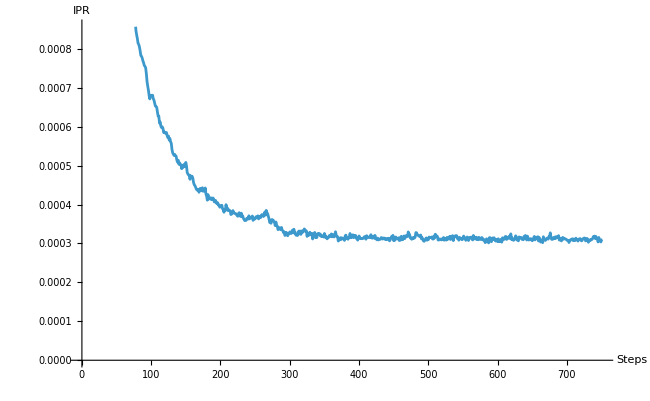

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Elipsis

```mathematica
Lx=70;Ly=50;
GrvAngle=Pi/4.;
GridData=GenerateEllipseBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedGroverCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
?NestList
```

```mathematica
(*
InitState=LocalizedState[GridData,{-20,10},{-1,-1,1,1}//Normalize]
*)
InitState=GaussianState[GridData,{-20,10},{-1,-1,1,1}//Normalize,1.5];
Steps=1500;
States=NestList[EvolOp.#&,InitState,Steps];
Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
PhasesWithoutFlatBands=Select[eigenphases,10^-5<Abs[#]<Pi-10^-5&];
FilteredPhases=Pick[PhasesWithoutFlatBands,Prepend[UnitStep[Differences[PhasesWithoutFlatBands]-10^-8],1],1];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## Cardiode

Dimension del operador evolución: 3692

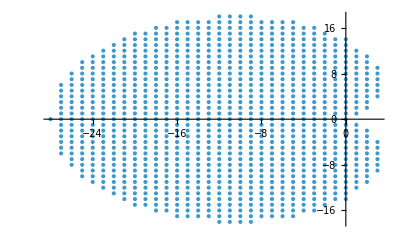

```mathematica
Lx=7;
GrvAngle=Pi/4.;
GridData=GenerateCardioidBasis[Lx];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedGroverCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{RandomInteger[{0,100}],RandomInteger[{0,70}]},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
PhasesWithoutFlatBands=Select[eigenphases,10^-5<Abs[#]<Pi-10^-5&];
FilteredPhases=Pick[PhasesWithoutFlatBands,Prepend[UnitStep[Differences[PhasesWithoutFlatBands]-10^-8],1],1];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

-Graphics-

## Haadamar Coin

## Rectangle

Dimension del operador evolución: 28684

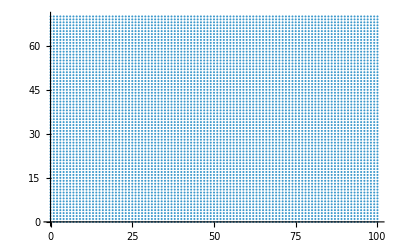

```mathematica
Lx=100;Ly=70;
GrvAngle=Pi/4.;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedHadamardCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
(*
InitState=LocalizedState[GridData,{20,10},{1,0,0,I}//Normalize];
*)
InitState=GaussianState[GridData,{50,35},{1,0,0,-1}//Normalize,1.5];
Steps=550;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Haad.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Ps_Rect_Haad.pdf",Img]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=170;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/SFF_Rect_Haad.pdf",Img]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=5000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Haad_RndPosCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_Haar.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

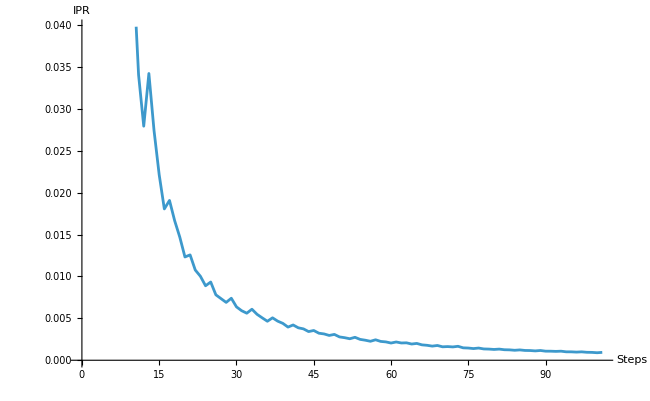

```mathematica
InitState=LocalizedState[GridData,{20,20},HaarRandomState[4]//Normalize];
Steps=100;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Sinai

Dimension del operador evolución: 18940

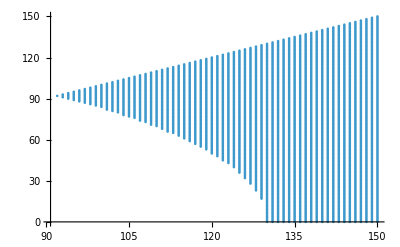

```mathematica
Lx=150;Ly=130;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedHadamardCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{55,30},HaarRandomState[4]//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Sinai_Haad.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Ps_Triangle_Haad.pdf",Img]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=170;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/SFF_Triangle_Haad.pdf",Img]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Sinai_Haad_RndPosCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_Haar.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

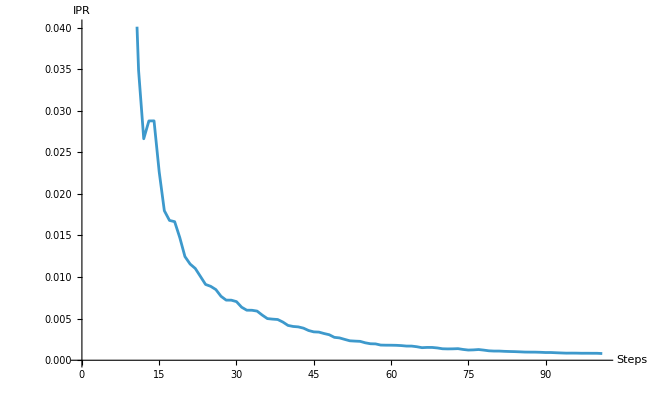

```mathematica
InitState=LocalizedState[GridData,{140,50},HaarRandomState[4]//Normalize];
Steps=100;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Fourier Coin

## Rectangle

```mathematica
Lx=100;Ly=70;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=FourierMatrix[4]//N;
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

Dimension del operador evolución: 28684

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{20,10},{-1,0,0,-1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

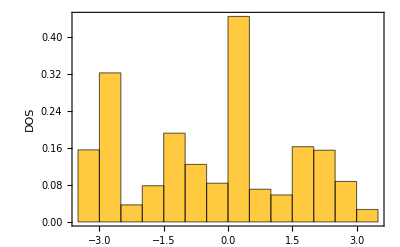

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

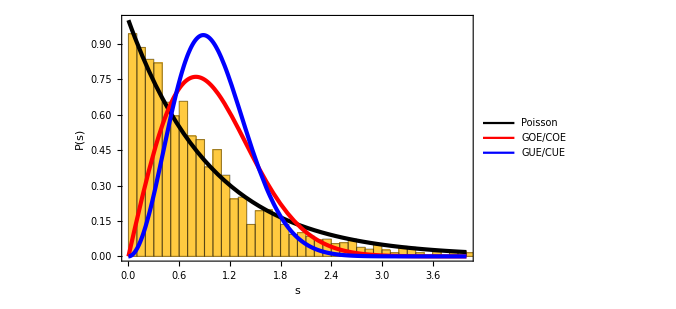

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

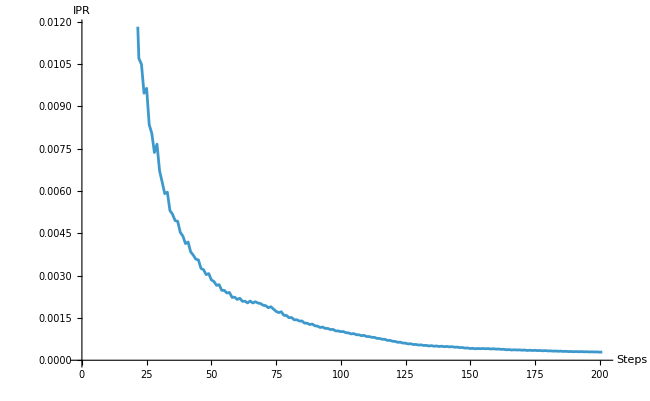

```mathematica
InitState=LocalizedState[GridData,{20,10},HaarRandomState[4]//Normalize];
Steps=200;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Sinai

Dimension del operador evolución: 3036

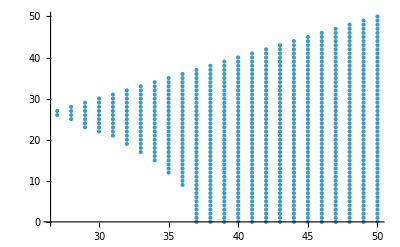

```mathematica
Lx=50;Ly=37;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=FourierMatrix[4]//N;
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Sinai.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{40,10},{-1,-1,1,1}//Normalize];
Steps=10;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

Part::partd: Part specification Frames⟦8⟧ is longer than depth of object.

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

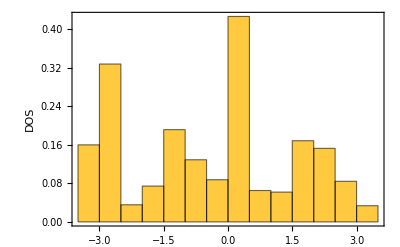

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Triangle_Grover.pdf",Img]
```

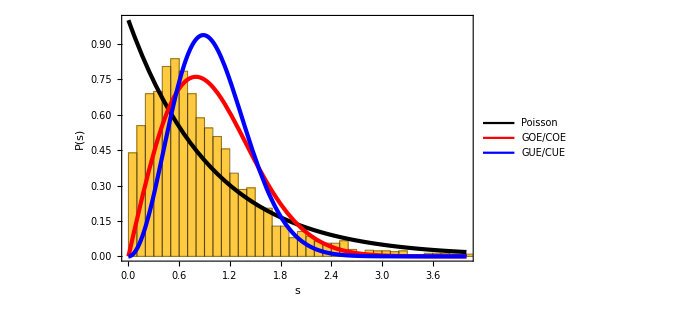

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

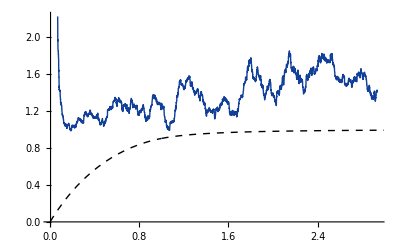

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Sinai_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_Chaos.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

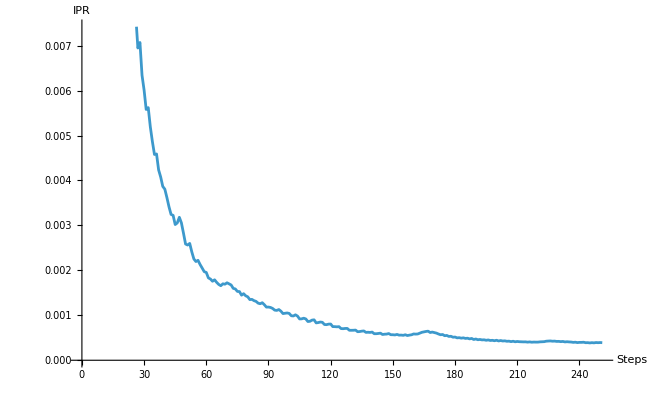

```mathematica
InitState=LocalizedState[GridData,{80,20},HaarRandomState[4]//Normalize];
Steps=250;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Elipsis

```mathematica
Lx=70;Ly=50;
GrvAngle=Pi/4.;
GridData=GenerateEllipseBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedGroverCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
?NestList
```

```mathematica
(*
InitState=LocalizedState[GridData,{-20,10},{-1,-1,1,1}//Normalize]
*)
InitState=GaussianState[GridData,{-20,10},{-1,-1,1,1}//Normalize,1.5];
Steps=1500;
States=NestList[EvolOp.#&,InitState,Steps];
Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
PhasesWithoutFlatBands=Select[eigenphases,10^-5<Abs[#]<Pi-10^-5&];
FilteredPhases=Pick[PhasesWithoutFlatBands,Prepend[UnitStep[Differences[PhasesWithoutFlatBands]-10^-8],1],1];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## Cardiode

```mathematica
Lx=7;
GridData=GenerateCardioidBasis[Lx];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=FourierMatrix[4]//N;
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

Dimension del operador evolución: 3692

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{RandomInteger[{0,100}],RandomInteger[{0,70}]},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

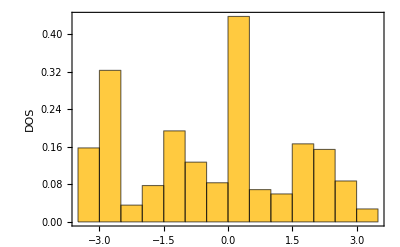

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

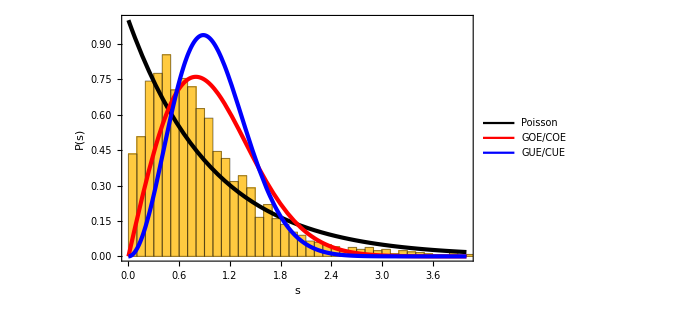

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

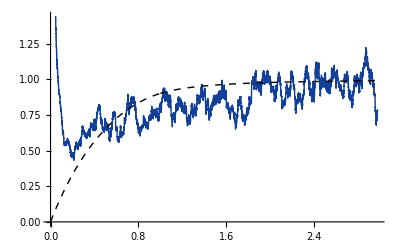

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

-Graphics-

## Cardiode (Sector de simetría)

```mathematica
(* ===1. Geometría:Cardioide===*)R=7;
GridData=GenerateCardioidBasis[R];
dim=GridData["Dimension"];

S=BuildShiftOperators[GridData,CoinDimension->4]; (*ajusta el nombre si en tu librería es BuildShiftOperators[...,CoinDimension->4]*)

(* ===2. Moneda:COE como línea base===*)
c=GeneralizedGroverCoin[Pi/4.]//N;
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=Chop[S.CoinOp];

(* ===3. Proyección al sector Cs===*)
sector="Even"; (*prueba también "Odd"*)
V1=BuildSymmetryIsometry[GridData,sector];

EvolOpSector=Chop[ConjugateTranspose[Normal[V1]].Normal[EvolOp].Normal[V1]];

Print["Dimension total: ",EvolOp//Length,"\n Dimension tomando el sector par: ",EvolOpSector//Length]
UnitaryMatrixQ[EvolOpSector]
```

Dimension total: 3692
 Dimension tomando el sector par: 1875

True

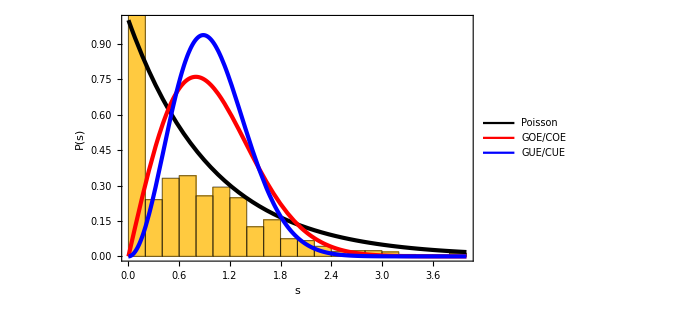

```mathematica
eigenphasesSector=Sort[Arg[Eigenvalues[EvolOpSector]]];
UnfoldedSector=Unfold[eigenphasesSector]["UnfoldedLevels"];
spacingsSector=Differences[UnfoldedSector//Sort,1];

EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
EmpiricalHistogramSector=Histogram[spacingsSector,"FreedmanDiaconis","PDF",PlotRange->{{0,4},{0,1}},Frame->True,FrameLabel->{"s","P(s)"},ImageSize->500,LabelStyle->Directive[Black,24]];
Show[EmpiricalHistogramSector,TheoreticalCurves]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{RandomInteger[{0,100}],RandomInteger[{0,70}]},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

-Graphics-

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

-Graphics-

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

-Graphics-

## Full Sinai

Dimension del operador evolución: 1728

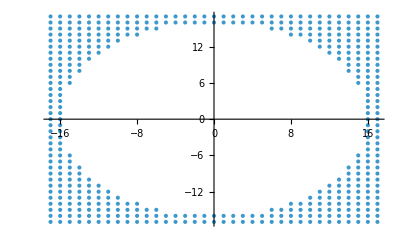

```mathematica
Lx=17;Ly=16;
GridData=GenerateFullSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=N[FourierMatrix[4]];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{RandomInteger[{0,100}],RandomInteger[{0,70}]},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

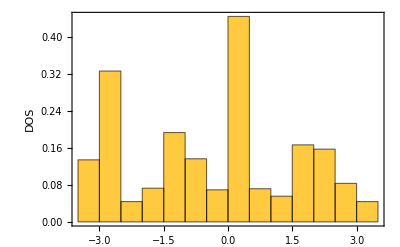

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

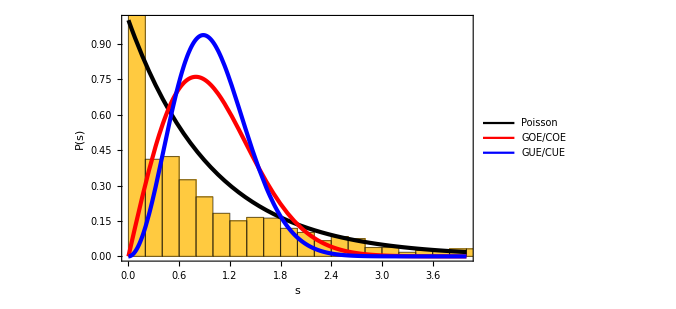

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

-Graphics-

## RandomCOE Coin

GENERAR LA MONEDA

```mathematica
c=RandomVariate[CircularOrthogonalMatrixDistribution[4]];
Chop[ConjugateTranspose[c].c]//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

## Rectangle

Dimension del operador evolución: 3224

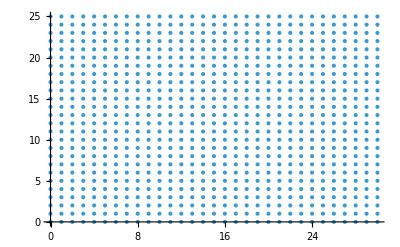

```mathematica
Lx=30;Ly=25;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=Chop[S.CoinOp];
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{10,50},HaarRandomState[4]//Normalize];
Steps=10;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

Part::partd: Part specification Frames⟦3⟧ is longer than depth of object.

### Spectral Statistic

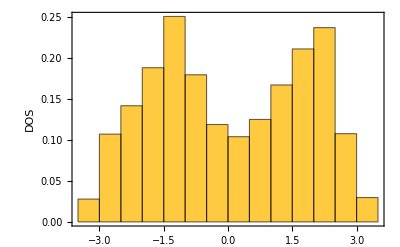

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_RndCOE.pdf",Img]
```

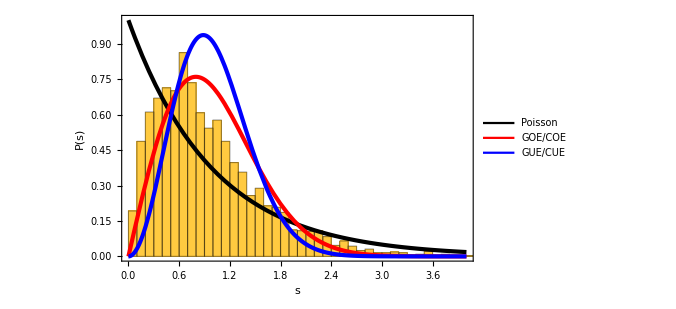

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};

TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];

  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Ps_Rect_RndCOE.pdf",Img]
```

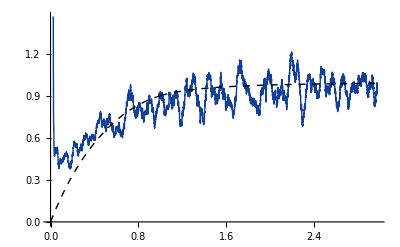

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/SFF_Rect_RndCOE.pdf",Img]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_COE_RndPosCoin.pdf",ImgD]
```

/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_COE_RndPosCoin.pdf

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RndCoin.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

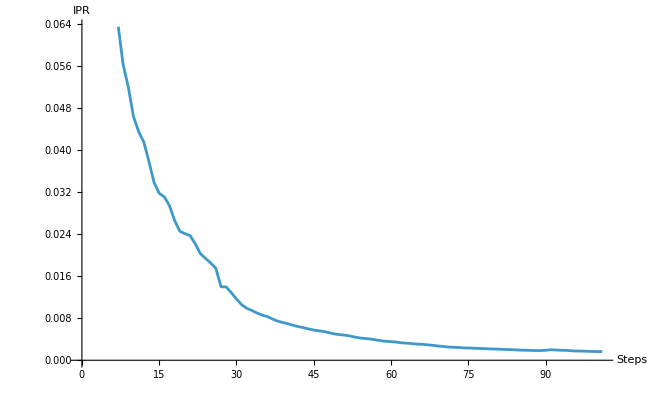

```mathematica
InitState=LocalizedState[GridData,{20,20},HaarRandomState[4]//Normalize];
Steps=100;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

#### Promediando sobre varios estados iniciales de moneda aleatorios

```mathematica
IPRTotal=Module[{InitState=LocalizedState[GridData,{20,20},HaarRandomState[4]//Normalize],Steps=100,States,Ipr},
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States];
```

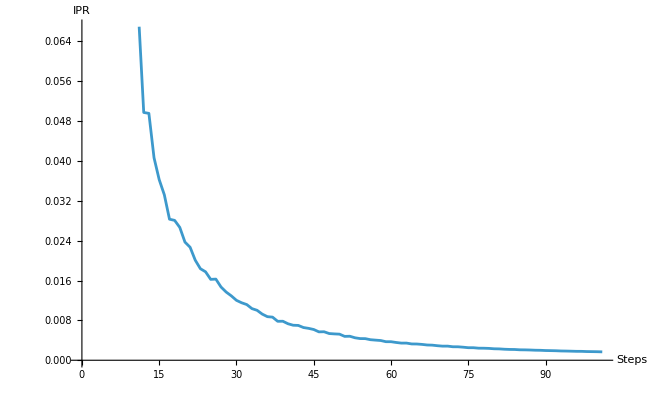

```mathematica
ListPlot[IPRTotal,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Sinai

Dimension del operador evolución: 1404

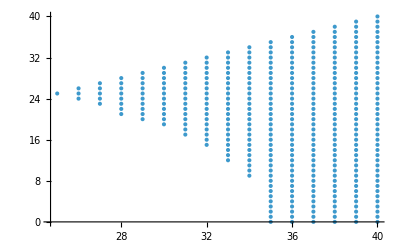

```mathematica
Lx=40;Ly=35;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{55,40},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

Part::partd: Part specification Frames⟦1⟧ is longer than depth of object.

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

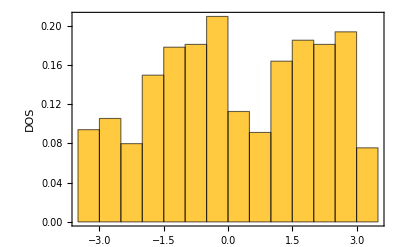

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Sinai_RndCOE.pdf",Img]
```

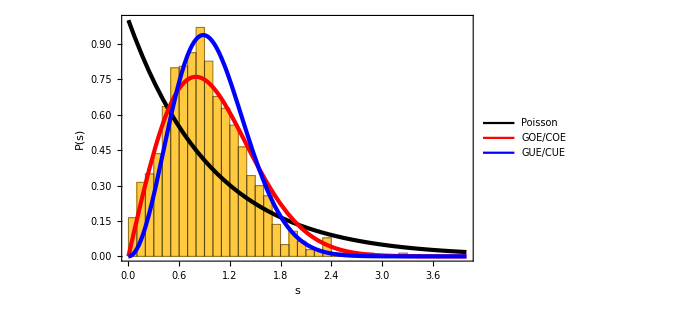

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Ps_Sinai_RndCOE.pdf",Img]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/SFF_Sinai_RndCOE.pdf",Img]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Sinai_COE_RndPosCoin.pdf",ImgD]
```

/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Sinai_COE_RndPosCoin.pdf

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_Haar.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

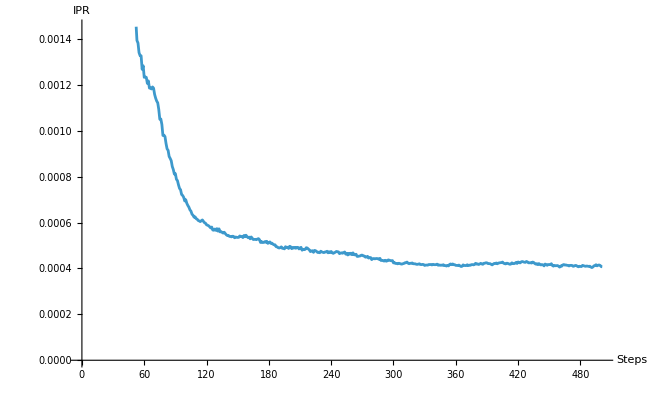

```mathematica
InitState=LocalizedState[GridData,{80,20},HaarRandomState[4]//Normalize];
Steps=500;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;

ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Random Coin

GENERAR LA MONEDA

```mathematica
matrizCompleja=RandomComplex[{-1-I,1+I},{4,4}];
c=Orthogonalize[matrizCompleja];

Chop[ConjugateTranspose[c].c]//MatrixForm
c//MatrixForm
```

## Rectangle

```mathematica
Lx=35;Ly=21;
GrvAngle=Pi/4.;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=Chop[S.CoinOp];
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{5,5},{-1,-1,1,1}//Normalize];
Steps=300;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};

TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];

  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=9000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistribution/RndCoin/LimitDistributionvsEvol_Rect_RndCoin_NotCOE.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## Sinai

```mathematica
Lx=45;Ly=0;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{55,20},{-1,-1,1,1}//Normalize];
Steps=500;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_Haar.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## Monedas aleatorias particulares:

### Cuyos eigenvalores sigan una estadística de Poisson.

```mathematica
Ndim=4;
evals=RandomReal[{0,2Pi},Ndim];
Unitevals=Exp[I*evals];
PoiDiagMat=DiagonalMatrix[Unitevals];
UnitMat=RandomVariate[CircularUnitaryMatrixDistribution[Ndim]];
RandomPoi=UnitMat.PoiDiagMat.ConjugateTranspose[UnitMat];
UnitaryMatrixQ[RandomPoi]
```

#### Pequeño chequeo que sí sigue poisson.

```mathematica
Ndim=500;
evals=RandomReal[{0,2Pi},Ndim];
Unitevals=Exp[I*evals];
PoiDiagMat=DiagonalMatrix[Unitevals];
UnitMat=FourierMatrix[Ndim];
RandomPoi=UnitMat.PoiDiagMat.ConjugateTranspose[UnitMat];
vals=Eigenvalues[RandomPoi];
phases=Arg[vals];
eigenPhases=Mod[#,2Pi]&/@phases;
difs=Differences[eigenPhases//Sort,1];
Histogram[difs,Automatic,"PDF"]
```

## Sinai

```mathematica
Lx=50;Ly=0;
GrvAngle=Pi/4.;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=RandomPoi;
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{35,20},HaarRandomState[4]//Normalize];
Steps=500;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=170;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Sinai_RndPoiWithCUE.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## VariableRandomCoin

La siguiente matriz varia ente 0 y 1 entre una unitaria con eigenvalores que siguen poisson hasta una unitaria que sigue COE.
M(0) -> Poisson
M(1)-> COE

```mathematica
dim=4;

(*---1. Inicialización (Tu código base)---*)
evals=RandomReal[{0,2 Pi},dim];
Unitevals=Exp[I*evals];
PoiDiagMat=DiagonalMatrix[Unitevals];
UnitMat=FourierMatrix[dim];
U1=RandomVariate[CircularUnitaryMatrixDistribution[dim]];
U0=UnitMat.PoiDiagMat.ConjugateTranspose[UnitMat];

V=U1.ConjugateTranspose[U0];
H=-I*MatrixLog[V];
M[t_]:=MatrixExp[I*H*t].U0;
```

## Rectangle

Dimension del operador evolución: 23004

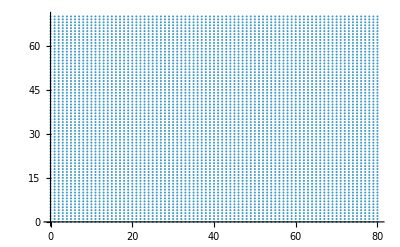

```mathematica
Lx=80;Ly=70;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];

t=1;
c=M[t];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=Chop[S.CoinOp];
Print["Dimension del operador evolución: ",EvolOp//Length]
ListPlot[GridData["Coords"]]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{31,30},HaarRandomState[4]//Normalize];
Steps=80;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};

TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];

  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=5000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_RandCoinChaos_RndPosCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistribution/RndCoin/LimitDistributionvsEvol_Rect_RndCoin_NotCOE.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

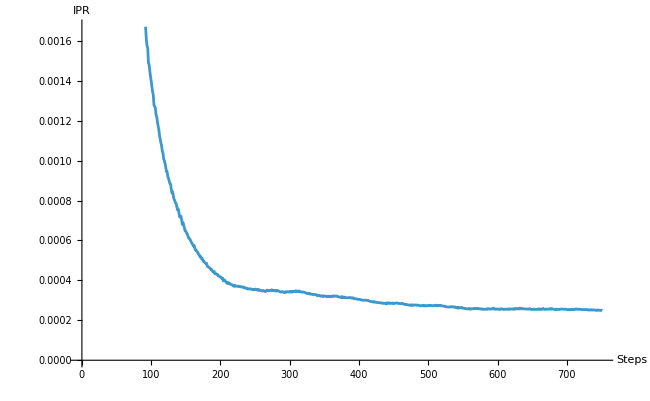

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

## Elipse

```mathematica
Lx=70;Ly=50;
GrvAngle=Pi/4.;
GridData=GenerateEllipseBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=GeneralizedHadamardCoin[GrvAngle];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

```mathematica
?GaussianState
```

### Visualización

```mathematica
(*
InitState=LocalizedState[GridData,{20,10},{1,0,0,I}//Normalize];
*)
InitState=GaussianState[GridData,{20,20},{1,0,0,1}//Normalize,1.5];
Steps=1500;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

### Spectral Statistic

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Img=Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Haad.pdf",Img]
```

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Ps_Rect_Haad.pdf",Img]
```

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=170;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/SFF_Rect_Haad.pdf",Img]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=5000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Haad_RndPosCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_Haar.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

## Separable Coin

```mathematica
C1=RandomVariate[CircularOrthogonalMatrixDistribution[2]];
C2=RandomVariate[CircularOrthogonalMatrixDistribution[2]];
c=KroneckerProduct[C1,C2];
```

## Rectangle

```mathematica
Lx=30;Ly=25;
GrvAngle=Pi/4.;
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
CoinOp=KroneckerProduct[IdentityMatrix[dim,SparseArray],c//SparseArray];
EvolOp=S.CoinOp;
Print["Dimension del operador evolución: ",EvolOp//Length]
Img=ListPlot[GridData["Coords"]]
```

Dimension del operador evolución: 3224

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/Stadium_Rect.pdf",Img]
```

### Visualización

```mathematica
InitState=LocalizedState[GridData,{5,5},{-1,-1,1,1}//Normalize];
Steps=50;
States=NestList[EvolOp.#&,InitState,Steps];

Frames=Rasterize[VisualizeWalkerState[GridData,#,"Linear",Automatic],RasterSize->600]&/@States;
Manipulate[Frames[[x]],{x,1,States//Length,1},AutoAction->True]
```

```mathematica
?Manipulate
```

```mathematica
Manipulate[Frames[[x]],{x,1,5,1}]
```

### Spectral Statistic

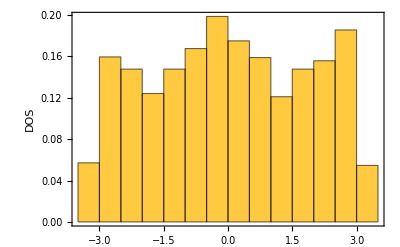

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/DoS_Rect_Grover.pdf",Img]
```

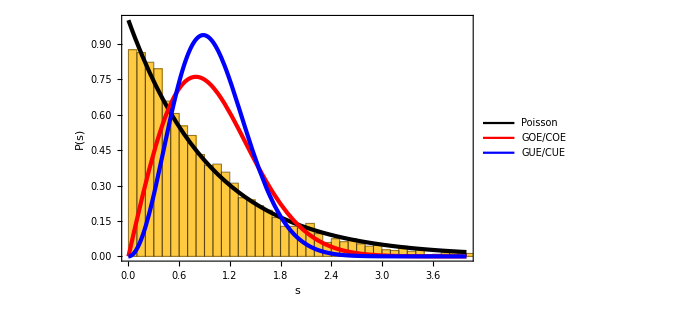

```mathematica
UnfoldedDat=Unfold[eigenphases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

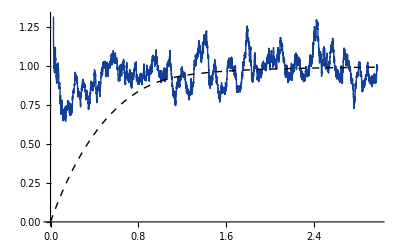

```mathematica
tmax=3;
DimSpace=Length[eigenphases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[eigenphases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=150;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Img=Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]]
```

```mathematica
Tmax=400;
InitState=LocalizedState[GridData,{17,10},HaarRandomState[4]//Normalize];
States=NestList[EvolOp.#&,InitState,Tmax];
TimeList=Range[1,Tmax,1];
IPRDataRect={#-1,ComputeSpatialIPR[States[[#]],4]}&/@TimeList;
EvenRect=Select[IPRDataRect,EvenQ[#[[1]]]&];
OddRect=Select[IPRDataRect,OddQ[#[[1]]]&];
Img=ListPlot[{EvenRect,OddRect},PlotRange->{{0,All},Automatic},PlotLegends->{"Tiempos pares","Tiempos impares"},LabelStyle->Directive[Bold, 15],Joined->{True,True},ImageSize->Large]
```

### Limit distribution

```mathematica
steps=7000;
FinalStates=NestList[EvolOp.#&,InitState,steps];
LimitCaseDat=LimitDistribution[FinalStates,4];
ImgD=DiscreteProbabilityPlot[GridData,LimitCaseDat,"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/saul/Desktop/EPS_QW/Chaos_Results/Imgs/LimitDist_Rect_Grover_RndPosSpecialCoin.pdf",ImgD]
```

#### Una pequeña comparación con un paper.

El paper de Inui et al. da un valor teórico para una red infinita, veamos que tanto se acerca a ese valor.

```mathematica
refVal=1/2+3/Pi^2-2/Pi;
distVal=Max[LimitCaseDat];
Print["El valor teórico: ",refVal," = ",refVal//N,"\n Valor calculado: ",distVal,"\n Diferencia porcentual: ",100*Abs[refVal-distVal]/refVal]
```

```mathematica
Tmax=7000;
steps=200;
Frames=DiscreteProbabilityPlot[GridData,LimitDistribution[NestList[EvolOp.#&,InitState,#],4],"ProbabilityScale"->"Linear",PlotLabel->"Quantum Walk Limit Distribution",ImageSize->Large]&/@Range[1,Tmax,steps];
ListAnimate[Frames,AnimationRunning->True,AnimationRate->1.5]
```

#### Exportacion

```mathematica
(*1. Aseguramos que la imagen fija tenga el mismo formato de renderizado*)
imgFijaRaster=Rasterize[ImgD,RasterSize->600];

(*2. Combinamos cada frame de la caminata con la imagen fija*)
(*Usamos GraphicsColumn para apilarlos verticalmente*)
framesFinales=Table[GraphicsColumn[{Frames[[i]],imgFijaRaster},Alignment->Center,Spacings->10],{i,1,Length[Frames]}];

(*3. Exportación final*)
Export["/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4",framesFinales,"FrameRate"->30]
```

```mathematica
"/Users/saul/Desktop/QWPics/4D/LimitDistributionvsEvol_Rect_RandCoin1.mp4"
```

### IPR

```mathematica
InitState=LocalizedState[GridData,{25,25},{1,1,-1,-1}//Normalize];
Steps=750;
States=NestList[EvolOp.#&,InitState,Steps];
IprDat=ComputeSpatialIPR[#,4]&/@States;
```

```mathematica
ListPlot[IprDat,AxesLabel->{"Steps", "IPR"},LabelStyle->Directive[Bold, 17],ImageSize->650,PlotRange->{All,Automatic},Joined->True]
```

-Graphics-